```mathematica
(*A1*)
l=RandomInteger[{10,25},7]
l^2
l^3
PrependTo[Table[{l[[i]],(l^2)[[i]],(l^3)[[i]]},{i,7}],{"numbers","Squares","cubes"}]//TableForm
sum=0;
Do[sum=sum+(l^2)[[i]],{i,7}]
sum
```

{24,11,21,22,13,18,10}

{576,121,441,484,169,324,100}

{13824,1331,9261,10648,2197,5832,1000}

Set::write: Tag Table in Table[{l⟦i⟧,l^2⟦i⟧,l^3⟦i⟧},{i,7}] is Protected.

numbers | Squares | cubes
24 | 576 | 13824
11 | 121 | 1331
21 | 441 | 9261
22 | 484 | 10648
13 | 169 | 2197
18 | 324 | 5832
10 | 100 | 1000

2215

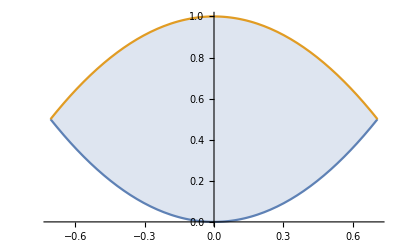

(2 √2)/3

20811/5

32/15 (-1+2 √2) π

```mathematica
(*A2*)
a=Solve[x^2==1-x^2][[1,1,2]];
b=Solve[x^2==1-x^2][[2,1,2]];
Plot[{x^2,1-x^2},{x,a,b},Filling->{1->{2}}]
∫_a^b (1-2 x^2)ⅆx
∫_0^3 ∫_0^2 ∫_0^(9 x^2+y^2) (9 x^2+y^2-z)ⅆzⅆyⅆx
∫_0^2 ∫_0^(√(4-y^2)) ∫_(√(x^2+y^2))^(√(8-x^2-y^2)) z^2 ⅆzⅆxⅆy
```

```mathematica
(*B1*)
F[x_,y_]=9 x^2-λ x y - 2 y^2-27 x + 18y;
a=9;
b=-2;
c=0;
f=18/2;
g=-27/2;
h=-λ/2;
d=({{a, h, g}, {h, b, f}, {g, f, c}});
Solve[Det[d]==0,λ]
```

{{λ→3}}

```mathematica
Factor[(F[x,y]/.λ->3)]
```

(3 x-2 y) (-9+3 x+y)

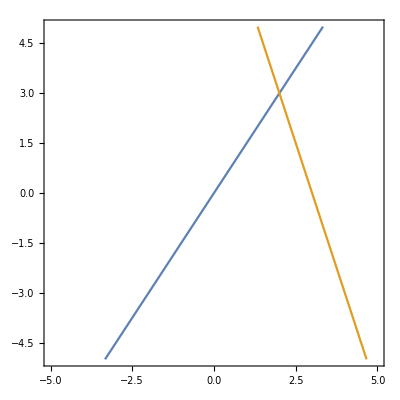

```mathematica
ContourPlot[{(3 x-2 y)==0, (-9+3 x+y)==0},{x,-5,5},{y,-5,5}]
```

```mathematica
(*B2*)
A=({{1, 3, 2}, {4, 2, 1}, {0, 3, 2}});
CharacteristicPolynomial[A,λ]
Solve[CharacteristicPolynomial[A,λ]==0,λ]
Eigenvectors[A]
```

1+7 λ+5 λ^2-λ^3

{{λ→-1},{λ→3-√10},{λ→3+√10}}

{{1/6 (4+√10),1/3 (1+√10),1},{1,-2,2},{1/6 (4-√10),1/3 (1-√10),1}}

```mathematica
IdentityMatrix[3]+7 A+5 MatrixPower[A,2]-MatrixPower[A,3]
```

{{0,0,0},{0,0,0},{0,0,0}}